```mathematica
(***Note: Values for generating these plots are embedded within the raw data set, which is too large to upload onto the public data repository***)
```

```mathematica
v1Color=RGBColor["#ff1f5b"];
```

```mathematica
lpColor=RGBColor["#009ade"];
```

```mathematica
lmColor=RGBColor["#f28522"];
```

```mathematica
controlColor=Black;
```

```mathematica
dateMouseListControl={{"012122","Mouse22550"},{"012822","Mouse22549"},{"121621","Mouse22525"},{"121721","Mouse22599"},{"011122","Mouse22598"},{"032923","Mouse23149"},{"033023","Mouse23128"},{"033123","Mouse23149"},{"070323","Mouse23149"},{"070423","Mouse23128"},{"070723","Mouse23128"}};
```

```mathematica
(***V1 axons, eOPN3***)
```

```mathematica
dateMouseListV1axons={{"012722","Mouse22504"},{"121821","Mouse22485"},{"062723","Mouse23154"},{"062723","Mouse23182"},{"063023","Mouse23154"},{"063023","Mouse23182"}};
```

```mathematica
(***LP axons, eOPN3***)
```

```mathematica
dateMouseListLPaxons={{"050123","Mouse23133"},{"050123","Mouse23142"},{"050323","Mouse23133"},{"050323","Mouse23142"},{"051823","Mouse23198"},{"052623","Mouse23198"},{"052623","Mouse23105"},{"062923","Mouse23139"},{"070223","Mouse23139"}};
```

```mathematica
(***LM axons, eOPN3***)
```

```mathematica
dateMouseListLMaxons={{"062623","Mouse23152"},{"062823","Mouse23152"},{"062923","Mouse23190"},{"070123","Mouse23190"},{"070723","Mouse23666"},{"071223","Mouse23666"}};
```

```mathematica
(************************************)
```

```mathematica
pairedROIsListControl=Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseListControl[[n,1]],"/",dateMouseListControl[[n,2]],"/PairedAnalysis/",dateMouseListControl[[n,1]],"_",dateMouseListControl[[n,2]],"_pairedROIsPupil.txt"],"List"],{n,1,Length[dateMouseListControl]}];
```

```mathematica
pairedROIsListV1axons=Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseListV1axons[[n,1]],"/",dateMouseListV1axons[[n,2]],"/PairedAnalysis/",dateMouseListV1axons[[n,1]],"_",dateMouseListV1axons[[n,2]],"_pairedROIsPupil.txt"],"List"],{n,1,Length[dateMouseListV1axons]}];
```

```mathematica
pairedROIsListLPaxons=Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseListLPaxons[[n,1]],"/",dateMouseListLPaxons[[n,2]],"/PairedAnalysis/",dateMouseListLPaxons[[n,1]],"_",dateMouseListLPaxons[[n,2]],"_pairedROIsPupil.txt"],"List"],{n,1,Length[dateMouseListLPaxons]}];
```

```mathematica
pairedROIsListLMaxons=Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseListLMaxons[[n,1]],"/",dateMouseListLMaxons[[n,2]],"/PairedAnalysis/",dateMouseListLMaxons[[n,1]],"_",dateMouseListLMaxons[[n,2]],"_pairedROIsPupil.txt"],"List"],{n,1,Length[dateMouseListLMaxons]}];
```

```mathematica
(**************)
```

```mathematica
whiskerCCControlDark=Table[Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseListControl[[n,1]],"/",dateMouseListControl[[n,2]],"/","Session1","/WhiskerData/",dateMouseListControl[[n,1]],"_",dateMouseListControl[[n,2]],"_","Session1","_","dFFwhiskCrossCorr_ROI",ToString[roi],".txt"],"List"],{roi,pairedROIsListControl[[n]]}],{n,1,Length[dateMouseListControl]}];
```

```mathematica
whiskerCCControlLED=Table[Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseListControl[[n,1]],"/",dateMouseListControl[[n,2]],"/","Session2","/WhiskerData/",dateMouseListControl[[n,1]],"_",dateMouseListControl[[n,2]],"_","Session2","_","dFFwhiskCrossCorr_ROI",ToString[roi],".txt"],"List"],{roi,pairedROIsListControl[[n]]}],{n,1,Length[dateMouseListControl]}];
```

```mathematica
whiskerCCV1axonsDark=Table[Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseListV1axons[[n,1]],"/",dateMouseListV1axons[[n,2]],"/","Session1","/WhiskerData/",dateMouseListV1axons[[n,1]],"_",dateMouseListV1axons[[n,2]],"_","Session1","_","dFFwhiskCrossCorr_ROI",ToString[roi],".txt"],"List"],{roi,pairedROIsListV1axons[[n]]}],{n,1,Length[dateMouseListV1axons]}];
```

```mathematica
whiskerCCV1axonsLED=Table[Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseListV1axons[[n,1]],"/",dateMouseListV1axons[[n,2]],"/","Session2","/WhiskerData/",dateMouseListV1axons[[n,1]],"_",dateMouseListV1axons[[n,2]],"_","Session2","_","dFFwhiskCrossCorr_ROI",ToString[roi],".txt"],"List"],{roi,pairedROIsListV1axons[[n]]}],{n,1,Length[dateMouseListV1axons]}];
```

```mathematica
whiskerCCLPaxonsDark=Table[Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseListLPaxons[[n,1]],"/",dateMouseListLPaxons[[n,2]],"/","Session1","/WhiskerData/",dateMouseListLPaxons[[n,1]],"_",dateMouseListLPaxons[[n,2]],"_","Session1","_","dFFwhiskCrossCorr_ROI",ToString[roi],".txt"],"List"],{roi,pairedROIsListLPaxons[[n]]}],{n,1,Length[dateMouseListLPaxons]}];
```

```mathematica
whiskerCCLPaxonsLED=Table[Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseListLPaxons[[n,1]],"/",dateMouseListLPaxons[[n,2]],"/","Session2","/WhiskerData/",dateMouseListLPaxons[[n,1]],"_",dateMouseListLPaxons[[n,2]],"_","Session2","_","dFFwhiskCrossCorr_ROI",ToString[roi],".txt"],"List"],{roi,pairedROIsListLPaxons[[n]]}],{n,1,Length[dateMouseListLPaxons]}];
```

```mathematica
whiskerCCLMaxonsDark=Table[Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseListLMaxons[[n,1]],"/",dateMouseListLMaxons[[n,2]],"/","Session1","/WhiskerData/",dateMouseListLMaxons[[n,1]],"_",dateMouseListLMaxons[[n,2]],"_","Session1","_","dFFwhiskCrossCorr_ROI",ToString[roi],".txt"],"List"],{roi,pairedROIsListLMaxons[[n]]}],{n,1,Length[dateMouseListLMaxons]}];
```

```mathematica
whiskerCCLMaxonsLED=Table[Table[ToExpression/@Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseListLMaxons[[n,1]],"/",dateMouseListLMaxons[[n,2]],"/","Session2","/WhiskerData/",dateMouseListLMaxons[[n,1]],"_",dateMouseListLMaxons[[n,2]],"_","Session2","_","dFFwhiskCrossCorr_ROI",ToString[roi],".txt"],"List"],{roi,pairedROIsListLMaxons[[n]]}],{n,1,Length[dateMouseListLMaxons]}];
```

```mathematica
catenatedWhiskCCControlDark=Flatten[whiskerCCControlDark,1];
```

```mathematica
catenatedWhiskCCControlLED=Flatten[whiskerCCControlLED,1];
```

```mathematica
catenatedWhiskCCV1axonsDark=Flatten[whiskerCCV1axonsDark,1];
```

```mathematica
catenatedWhiskCCV1axonsLED=Flatten[whiskerCCV1axonsLED,1];
```

```mathematica
catenatedWhiskCCLPaxonsDark=Flatten[whiskerCCLPaxonsDark,1];
```

```mathematica
catenatedWhiskCCLPaxonsLED=Flatten[whiskerCCLPaxonsLED,1];
```

```mathematica
catenatedWhiskCCLMaxonsDark=Flatten[whiskerCCLMaxonsDark,1];
```

```mathematica
catenatedWhiskCCLMaxonsLED=Flatten[whiskerCCLMaxonsLED,1];
```

```mathematica
(**************)
```

```mathematica
(***)
```

```mathematica
meanCatenatedWhiskCCControlDark=Mean[catenatedWhiskCCControlDark];
```

```mathematica
semCatenatedWhiskCCControlDark=(#/Sqrt@Length[catenatedWhiskCCControlDark])&/@StandardDeviation[catenatedWhiskCCControlDark];
```

```mathematica
(***)
```

```mathematica
meanCatenatedWhiskCCV1axonsDark=Mean[catenatedWhiskCCV1axonsDark];
```

```mathematica
semCatenatedWhiskCCV1axonsDark=(#/Sqrt@Length[catenatedWhiskCCV1axonsDark])&/@StandardDeviation[catenatedWhiskCCV1axonsDark];
```

```mathematica
(***)
```

```mathematica
meanCatenatedWhiskCCLPaxonsDark=Mean[catenatedWhiskCCLPaxonsDark];
```

```mathematica
semCatenatedWhiskCCLPaxonsDark=(#/Sqrt@Length[catenatedWhiskCCLPaxonsDark])&/@StandardDeviation[catenatedWhiskCCLPaxonsDark];
```

```mathematica
(***)
```

```mathematica
meanCatenatedWhiskCCLMaxonsDark=Mean[catenatedWhiskCCLMaxonsDark];
```

```mathematica
semCatenatedWhiskCCLMaxonsDark=(#/Sqrt@Length[catenatedWhiskCCLMaxonsDark])&/@StandardDeviation[catenatedWhiskCCLMaxonsDark];
```

```mathematica
(***)
```

```mathematica
meanCatenatedWhiskCCControlLED=Mean[catenatedWhiskCCControlLED];
```

```mathematica
semCatenatedWhiskCCControlLED=(#/Sqrt@Length[catenatedWhiskCCControlLED])&/@StandardDeviation[catenatedWhiskCCControlLED];
```

```mathematica
(***)
```

```mathematica
meanCatenatedWhiskCCV1axonsLED=Mean[catenatedWhiskCCV1axonsLED];
```

```mathematica
semCatenatedWhiskCCV1axonsLED=(#/Sqrt@Length[catenatedWhiskCCV1axonsLED])&/@StandardDeviation[catenatedWhiskCCV1axonsLED];
```

```mathematica
(***)
```

```mathematica
meanCatenatedWhiskCCLPaxonsLED=Mean[catenatedWhiskCCLPaxonsLED];
```

```mathematica
semCatenatedWhiskCCLPaxonsLED=(#/Sqrt@Length[catenatedWhiskCCLPaxonsLED])&/@StandardDeviation[catenatedWhiskCCLPaxonsLED];
```

```mathematica
(***)
```

```mathematica
meanCatenatedWhiskCCLMaxonsLED=Mean[catenatedWhiskCCLMaxonsLED];
```

```mathematica
semCatenatedWhiskCCLMaxonsLED=(#/Sqrt@Length[catenatedWhiskCCLMaxonsLED])&/@StandardDeviation[catenatedWhiskCCLMaxonsLED];
```

```mathematica
(**************)
```

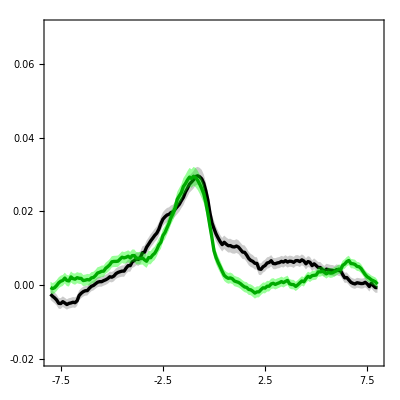

```mathematica
Show[ListLinePlot[{Part[#,2]&/@meanCatenatedWhiskCCControlDark,Part[#,2]&/@meanCatenatedWhiskCCControlDark+(Part[#,2]&/@semCatenatedWhiskCCControlDark),Part[#,2]&/@meanCatenatedWhiskCCControlDark-(Part[#,2]&/@semCatenatedWhiskCCControlDark)},Filling->{1->{{2},Directive[Opacity[0.4],Gray]},1->{{3},Directive[Opacity[0.4],Gray]}},PlotStyle->{{Black,Thickness[0.006]},Transparent,Transparent},DataRange->{-8,8},PlotRange->{{-8,8},{-0.02,0.07}},FrameTicks->{{LinTicks[-0.02,0.07,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[-8,8,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]],ListLinePlot[{Part[#,2]&/@meanCatenatedWhiskCCControlLED,Part[#,2]&/@meanCatenatedWhiskCCControlLED+(Part[#,2]&/@semCatenatedWhiskCCControlLED),Part[#,2]&/@meanCatenatedWhiskCCControlLED-(Part[#,2]&/@semCatenatedWhiskCCControlLED)},Filling->{1->{{2},Directive[Opacity[0.4],Green]},1->{{3},Directive[Opacity[0.4],Green]}},PlotStyle->{{Darker@Green,Thickness[0.006]},Transparent,Transparent},DataRange->{-8,8},PlotRange->{{-8,8},{-0.02,0.07}},FrameTicks->{{LinTicks[-0.02,0.07,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[-8,8,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]],AspectRatio->1]
```

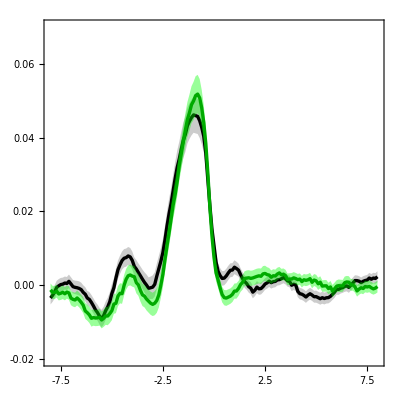

```mathematica
Show[ListLinePlot[{Part[#,2]&/@meanCatenatedWhiskCCV1axonsDark,Part[#,2]&/@meanCatenatedWhiskCCV1axonsDark+(Part[#,2]&/@semCatenatedWhiskCCV1axonsDark),Part[#,2]&/@meanCatenatedWhiskCCV1axonsDark-(Part[#,2]&/@semCatenatedWhiskCCV1axonsDark)},Filling->{1->{{2},Directive[Opacity[0.4],Gray]},1->{{3},Directive[Opacity[0.4],Gray]}},PlotStyle->{{Black,Thickness[0.006]},Transparent,Transparent},DataRange->{-8,8},PlotRange->{{-8,8},{-0.02,0.07}},FrameTicks->{{LinTicks[-0.02,0.07,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[-8,8,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]],ListLinePlot[{Part[#,2]&/@meanCatenatedWhiskCCV1axonsLED,Part[#,2]&/@meanCatenatedWhiskCCV1axonsLED+(Part[#,2]&/@semCatenatedWhiskCCV1axonsLED),Part[#,2]&/@meanCatenatedWhiskCCV1axonsLED-(Part[#,2]&/@semCatenatedWhiskCCV1axonsLED)},Filling->{1->{{2},Directive[Opacity[0.4],Green]},1->{{3},Directive[Opacity[0.4],Green]}},PlotStyle->{{Darker@Green,Thickness[0.006]},Transparent,Transparent},DataRange->{-8,8},PlotRange->{{-8,8},{-0.02,0.07}},FrameTicks->{{LinTicks[-0.02,0.07,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[-8,8,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]],AspectRatio->1]
```

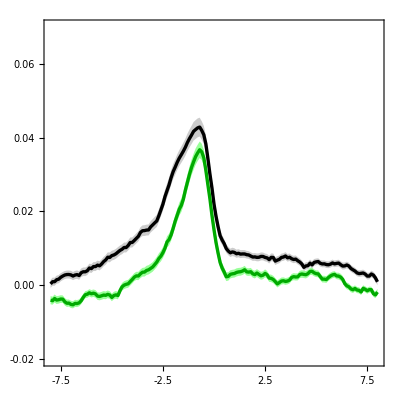

```mathematica
Show[ListLinePlot[{Part[#,2]&/@meanCatenatedWhiskCCLPaxonsDark,Part[#,2]&/@meanCatenatedWhiskCCLPaxonsDark+(Part[#,2]&/@semCatenatedWhiskCCLPaxonsDark),Part[#,2]&/@meanCatenatedWhiskCCLPaxonsDark-(Part[#,2]&/@semCatenatedWhiskCCLPaxonsDark)},Filling->{1->{{2},Directive[Opacity[0.4],Gray]},1->{{3},Directive[Opacity[0.4],Gray]}},PlotStyle->{{Black,Thickness[0.006]},Transparent,Transparent},DataRange->{-8,8},PlotRange->{{-8,8},{-0.02,0.07}},FrameTicks->{{LinTicks[-0.02,0.07,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[-8,8,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]],ListLinePlot[{Part[#,2]&/@meanCatenatedWhiskCCLPaxonsLED,Part[#,2]&/@meanCatenatedWhiskCCLPaxonsLED+(Part[#,2]&/@semCatenatedWhiskCCLPaxonsLED),Part[#,2]&/@meanCatenatedWhiskCCLPaxonsLED-(Part[#,2]&/@semCatenatedWhiskCCLPaxonsLED)},Filling->{1->{{2},Directive[Opacity[0.4],Green]},1->{{3},Directive[Opacity[0.4],Green]}},PlotStyle->{{Darker@Green,Thickness[0.006]},Transparent,Transparent},DataRange->{-8,8},PlotRange->{{-8,8},{-0.02,0.07}},FrameTicks->{{LinTicks[-0.02,0.07,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[-8,8,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]],AspectRatio->1]
```

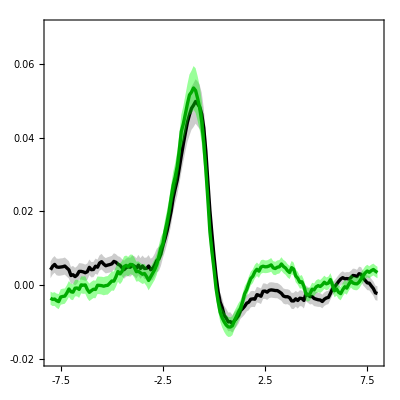

```mathematica
Show[ListLinePlot[{Part[#,2]&/@meanCatenatedWhiskCCLMaxonsDark,Part[#,2]&/@meanCatenatedWhiskCCLMaxonsDark+(Part[#,2]&/@semCatenatedWhiskCCLMaxonsDark),Part[#,2]&/@meanCatenatedWhiskCCLMaxonsDark-(Part[#,2]&/@semCatenatedWhiskCCLMaxonsDark)},Filling->{1->{{2},Directive[Opacity[0.4],Gray]},1->{{3},Directive[Opacity[0.4],Gray]}},PlotStyle->{{Black,Thickness[0.006]},Transparent,Transparent},DataRange->{-8,8},PlotRange->{{-8,8},{-0.02,0.07}},FrameTicks->{{LinTicks[-0.02,0.07,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[-8,8,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]],ListLinePlot[{Part[#,2]&/@meanCatenatedWhiskCCLMaxonsLED,Part[#,2]&/@meanCatenatedWhiskCCLMaxonsLED+(Part[#,2]&/@semCatenatedWhiskCCLMaxonsLED),Part[#,2]&/@meanCatenatedWhiskCCLMaxonsLED-(Part[#,2]&/@semCatenatedWhiskCCLMaxonsLED)},Filling->{1->{{2},Directive[Opacity[0.4],Green]},1->{{3},Directive[Opacity[0.4],Green]}},PlotStyle->{{Darker@Green,Thickness[0.006]},Transparent,Transparent},DataRange->{-8,8},PlotRange->{{-8,8},{-0.02,0.07}},FrameTicks->{{LinTicks[-0.02,0.07,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[-8,8,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,Frame->{{True,None},{True,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]],AspectRatio->1]
```